## Loop

```mathematica
Loop:=(For[


Array[AlleleFreqA,Nloci];
Array[AlleleFreqB,Nloci];
Do[AlleleFreqA[i]={},{i,1,Nloci}];
Do[AlleleFreqB[i]={},{i,1,Nloci}];
TotalLoadA={};
TotalLoadB={};


DiploidFitnessTable=Table[1,{i,NHaplotypes},{j,NHaplotypes}];

Do[
If[BitGet[BitOr[i-1,j-1],1]-BitGet[BitOr[i-1,j-1],2]== 0,DiploidFitnessTable[[i,j]]*=1,DiploidFitnessTable[[i,j]]*=tox];
If[BitGet[i-1,1]+BitGet[j-1,1]==1,DiploidFitnessTable[[i,j]]*=(1-sc)^(1/2),If[BitGet[i-1,1]+BitGet[j-1,1]==2,DiploidFitnessTable[[i,j]]*=(1-sc),DiploidFitnessTable[[i,j]]*=1]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

Do[
If[(BitGet[i-1,1]+BitGet[j-1,1])>0,
If[BitGet[i-1,0]+BitGet[j-1,0]==1,DiploidFitnessTable[[i,j]]*=h1]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

ViabilitySelection=DiploidFitnessTable;
Do[
If[(BitGet[i-1,0]+BitGet[j-1,0])==1,ViabilitySelection[[i,j]]*=(1-sp)^(1/2),
If[(BitGet[i-1,0]+BitGet[j-1,0])==2,ViabilitySelection[[i,j]]*=(1-sp)]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

MaskProb=Function[{mask,Nloci},
For[prob=1.0;z=1, z<Nloci,z++,
If[BitGet[mask,(Nloci-z)]==BitGet[mask,(Nloci-z-1)],
prob*=(1-recrate[z]),
prob*=recrate[z]]]];

ZygoteGenotypes=Function[{i,j,mask},
For[zyg1=0;zyg2=0;k=0,k<Nloci,k++,
If[BitGet[mask,k]==0,
zyg1=BitOr[zyg1,(BitAnd[i,(2^k)])];zyg2=BitOr[zyg2,(BitAnd[j,(2^k)])],
zyg1=BitOr[zyg1,(BitAnd[j,(2^k)])];zyg2=BitOr[zyg2,(BitAnd[i,(2^k)])]]]];

RecTable=Table[0,{i,NHaplotypes},{j,NHaplotypes},{k,NHaplotypes}];
For[i=0,i<NHaplotypes,i++,
For[j=0,j<NHaplotypes,j++,
For[mask=0,mask<masklim,mask++,
MaskProb[mask,Nloci];
zygoteProb =0.5*prob;
ZygoteGenotypes[i,j,mask];
RecTable[[(i+1),(j+1),(zyg1+1)]]+=zygoteProb;
RecTable[[(i+1),(j+1),(zyg2+1)]]+=zygoteProb;]]];


g=0,g<Generations+1,g++,


GenoFreqSelecA=GenoFreqA*ViabilitySelection/Total[GenoFreqA*ViabilitySelection,2];
GenoFreqSelecB=GenoFreqB*ViabilitySelection/Total[GenoFreqB*ViabilitySelection,2];

TotalLoadt1A=1-Total[GenoFreqA*ViabilitySelection,2];
TotalLoadt1B=1-Total[GenoFreqB*ViabilitySelection,2];
LoadAtoBRatio=(1-TotalLoadt1A)/(1-TotalLoadt1B);

GenoFreqMigrA=GenoFreqSelecA;
GenoFreqMigrB=GenoFreqSelecB;

Do[GenoFreqMigrA[[i,j]]+=GenoFreqSelecB[[i,j]]*μA/LoadAtoBRatio;,{i,1,NHaplotypes},{j,1,NHaplotypes}];
Do[GenoFreqMigrB[[i,j]]+=GenoFreqSelecA[[i,j]]*μB*LoadAtoBRatio;,{i,1,NHaplotypes},{j,1,NHaplotypes}];

GenoFreqSelecA=GenoFreqMigrA/Total[GenoFreqMigrA,2];
GenoFreqSelecB=GenoFreqMigrB/Total[GenoFreqMigrB,2];


If[g==0,
GenoFreqSelecA[[1,1]]=1-IntroFreq1-IntroFreq2;
GenoFreqSelecA[[7,7]]=IntroFreq1;
GenoFreqSelecA[[NHaplotypes,NHaplotypes]]=IntroFreq2;
GenoFreqSelecA=GenoFreqSelecA/(Total[GenoFreqSelecA,2])];

Do[k=i;l=j;If [BitGet[BitOr[i,j],1]==1,If[(BitGet[i,0]+BitGet[j,0])==1,k=BitSet[k,0];l=BitSet[l,0];
GenoFreqSelecA[[k+1,l+1]]+=GenoFreqSelecA[[i+1,j+1]];GenoFreqSelecA[[i+1,j+1]]=0;
]],{i,0,NHaplotypes-1},{j,0,NHaplotypes-1}];

Do[k=i;l=j;If [BitGet[BitOr[i,j],1]==1,If[(BitGet[i,0]+BitGet[j,0])==1,k=BitSet[k,0];l=BitSet[l,0];
GenoFreqSelecB[[k+1,l+1]]+=GenoFreqSelecB[[i+1,j+1]];GenoFreqSelecB[[i+1,j+1]]=0;
]],{i,0,NHaplotypes-1},{j,0,NHaplotypes-1}];


GameteTableA=RecTable*GenoFreqSelecA;
GameteTableB=RecTable*GenoFreqSelecB;

HaploFreqt1A=Total[GameteTableA,2];
HaploFreqt1B=Total[GameteTableB,2];

HaploFreqA=HaploFreqt1A/(Total[HaploFreqt1A]);
HaploFreqB=HaploFreqt1B/(Total[HaploFreqt1B]);

GenoFreqT1A=KroneckerProduct[HaploFreqA,HaploFreqA];
GenoFreqT1B=KroneckerProduct[HaploFreqB,HaploFreqB];

GenoFreqA=GenoFreqT1A;
GenoFreqB=GenoFreqT1B;

Do[AlleleFreqT1A[i]=0,{i,1,Nloci}];
Do[If[BitGet[j-1,i-1]==1,AlleleFreqT1A[i]+=HaploFreqA[[j]]],{i,1,Nloci},{j,1,NHaplotypes}];

Do[AlleleFreqT1B[i]=0,{i,1,Nloci}];
Do[If[BitGet[j-1,i-1]==1,AlleleFreqT1B[i]+=HaploFreqB[[j]]],{i,1,Nloci},{j,1,NHaplotypes}];

Do[AppendTo[AlleleFreqA[i],AlleleFreqT1A[i]],{i,1,Nloci}];
Do[AppendTo[AlleleFreqB[i],AlleleFreqT1B[i]],{i,1,Nloci}];


])
```

## Figures

### μ = 1%, sp = 0.05

```mathematica
Nloci=3;
NGenotypes=3^Nloci; NHaplotypes=2^Nloci;
recrate[1]=0.5; recrate[2]=0.5;
masklim=2^(Nloci-1);
tox=0;(*this describes the level of toxicity for the underdominance toxins. 1 is no effect on fitness, 0 is complete lethality *)
thresh=.; (*this is the delay, in # of generations, for the 2nd introduction*)

Generations=100;
h1=.95;
sc=0.05;
sp=0.05;

μ=0.01;
IntroFreqTotal=0.5;

μA=μ; μB=μ;
IntroFreq2=0.05;
IntroFreq1=(IntroFreqTotal-IntroFreq2);

GenoFreqA=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqA[[1,1]]=1;
GenoFreqB=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqB[[1,1]]=1;
```

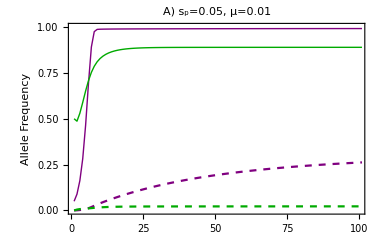

```mathematica
Loop;Fig1=ListPlot[{AlleleFreqA[1],AlleleFreqA[2],AlleleFreqB[1],AlleleFreqB[2]},FrameLabel->{None," Allele Frequency"},PlotLabel->Style["A) s_p=0.05, μ=0.01",20,Black],
PlotRange->{{1,Generations},{0,1.000000000000001}},Joined->True,Frame->{True,True,False,False},PlotStyle->{Directive[Purple, Thick],Directive[Darker[Green], Thick],Directive[Purple, Dashed],Directive[Darker[Green], Dashed]},FrameStyle->Directive[20,Black],ImageSize->{380,250}]
```

### μ = 5%, sp = 0.05

```mathematica
Nloci=3;
NGenotypes=3^Nloci; NHaplotypes=2^Nloci;
recrate[1]=0.5; recrate[2]=0.5;
masklim=2^(Nloci-1);
tox=0;(*this describes the level of toxicity for the underdominance toxins. 1 is no effect on fitness, 0 is complete lethality *)
thresh=.; (*this is the delay, in # of generations, for the 2nd introduction*)

Generations=100;
h1=.95;
sc=0.05;
sp=0.05;

μ=0.05;
IntroFreqTotal=0.5;

μA=μ; μB=μ;
IntroFreq2=0.05;
IntroFreq1=(IntroFreqTotal-IntroFreq2);

GenoFreqA=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqA[[1,1]]=1;
GenoFreqB=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqB[[1,1]]=1;
```

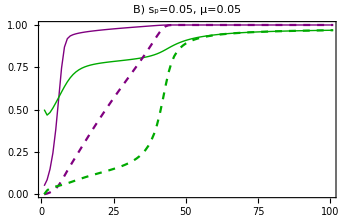

```mathematica
Loop;Fig2=ListPlot[{AlleleFreqA[1],AlleleFreqA[2],AlleleFreqB[1],AlleleFreqB[2]},PlotLabel->Style["B) s_p=0.05, μ=0.05",20,Black],
PlotRange->{{1,Generations},{0,1.000000000000001}},Joined->True,Frame->{True,True,False,False},PlotStyle->{Directive[Purple, Thick],Directive[Darker[Green], Thick],Directive[Purple, Dashed],Directive[Darker[Green], Dashed]},FrameStyle->Directive[20,Black],ImageSize->{350,250}]
```

### μ = 1%, sp = 0.3

```mathematica
Nloci=3;
NGenotypes=3^Nloci; NHaplotypes=2^Nloci;
recrate[1]=0.5; recrate[2]=0.5;
masklim=2^(Nloci-1);
tox=0;(*this describes the level of toxicity for the underdominance toxins. 1 is no effect on fitness, 0 is complete lethality *)
thresh=.; (*this is the delay, in # of generations, for the 2nd introduction*)

Generations=100;
h1=.95;
sc=0.05;
sp=0.3;

μ=0.01;
IntroFreqTotal=0.5;

μA=μ; μB=μ;
IntroFreq2=0.05;
IntroFreq1=(IntroFreqTotal-IntroFreq2);

GenoFreqA=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqA[[1,1]]=1;
GenoFreqB=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqB[[1,1]]=1;
```

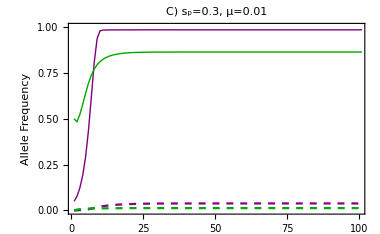

```mathematica
Loop;Fig3=ListPlot[{AlleleFreqA[1],AlleleFreqA[2],AlleleFreqB[1],AlleleFreqB[2]},FrameLabel->{None," Allele Frequency"},PlotLabel->Style["C) s_p=0.3, μ=0.01",20,Black],
PlotRange->{{1,Generations},{0,1.000000000000001}},Joined->True,Frame->{True,True,False,False},PlotStyle->{Directive[Purple, Thick],Directive[Darker[Green], Thick],Directive[Purple, Dashed],Directive[Darker[Green], Dashed]},FrameStyle->Directive[20,Black],ImageSize->{380,250}]
```

### μ = 5%, sp = 0.3

```mathematica
Nloci=3;
NGenotypes=3^Nloci; NHaplotypes=2^Nloci;
recrate[1]=0.5; recrate[2]=0.5;
masklim=2^(Nloci-1);
tox=0;(*this describes the level of toxicity for the underdominance toxins. 1 is no effect on fitness, 0 is complete lethality *)
thresh=.; (*this is the delay, in # of generations, for the 2nd introduction*)

Generations=100;
h1=.95;
sc=0.05;
sp=0.3;

μ=0.05;
IntroFreqTotal=0.5;

μA=μ; μB=μ;
IntroFreq2=0.05;
IntroFreq1=(IntroFreqTotal-IntroFreq2);

GenoFreqA=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqA[[1,1]]=1;
GenoFreqB=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqB[[1,1]]=1;
```

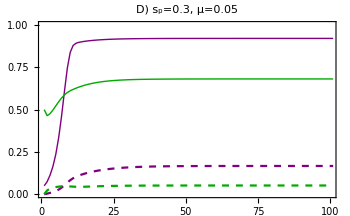

```mathematica
Loop;Fig4=ListPlot[{AlleleFreqA[1],AlleleFreqA[2],AlleleFreqB[1],AlleleFreqB[2]},PlotLabel->Style["D) s_p=0.3, μ=0.05",20,Black],
PlotRange->{{1,Generations},{0,1.000000000000001}},Joined->True,Frame->{True,True,False,False},PlotStyle->{Directive[Purple, Thick],Directive[Darker[Green], Thick],Directive[Purple, Dashed],Directive[Darker[Green], Dashed]},FrameStyle->Directive[20,Black],ImageSize->{350,250}]
```

### μ = 1%, sp = 0.7

```mathematica
Nloci=3;
NGenotypes=3^Nloci; NHaplotypes=2^Nloci;
recrate[1]=0.5; recrate[2]=0.5;
masklim=2^(Nloci-1);
tox=0;(*this describes the level of toxicity for the underdominance toxins. 1 is no effect on fitness, 0 is complete lethality *)
thresh=.; (*this is the delay, in # of generations, for the 2nd introduction*)

Generations=100;
h1=.95;
sc=0.05;
sp=0.7;

μ=0.01;
IntroFreqTotal=0.5;

μA=μ; μB=μ;
IntroFreq2=0.05;
IntroFreq1=(IntroFreqTotal-IntroFreq2);

GenoFreqA=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqA[[1,1]]=1;
GenoFreqB=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqB[[1,1]]=1;
```

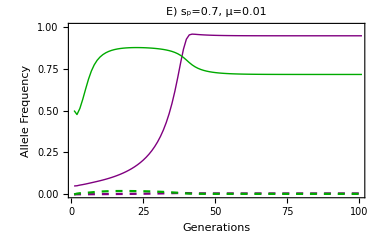

```mathematica
Loop;Fig5=ListPlot[{AlleleFreqA[1],AlleleFreqA[2],AlleleFreqB[1],AlleleFreqB[2]},FrameLabel->{"Generations"," Allele Frequency"},PlotLabel->Style["E) s_p=0.7, μ=0.01",20,Black],
PlotRange->{{1,Generations},{0,1.000000000000001}},Joined->True,Frame->{True,True,False,False},PlotStyle->{Directive[Purple, Thick],Directive[Darker[Green], Thick],Directive[Purple, Dashed],Directive[Darker[Green], Dashed]},FrameStyle->Directive[20,Black],ImageSize->{380,280}]
```

### μ = 5%, sp = 0.7

```mathematica
Nloci=3;
NGenotypes=3^Nloci; NHaplotypes=2^Nloci;
recrate[1]=0.5; recrate[2]=0.5;
masklim=2^(Nloci-1);
tox=0;(*this describes the level of toxicity for the underdominance toxins. 1 is no effect on fitness, 0 is complete lethality *)
thresh=.; (*this is the delay, in # of generations, for the 2nd introduction*)

Generations=100;
h1=.95;
sc=0.05;
sp=0.7;

μ=0.05;
IntroFreqTotal=0.5;

μA=μ; μB=μ;
IntroFreq2=0.05;
IntroFreq1=(IntroFreqTotal-IntroFreq2);

GenoFreqA=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqA[[1,1]]=1;
GenoFreqB=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqB[[1,1]]=1;
```

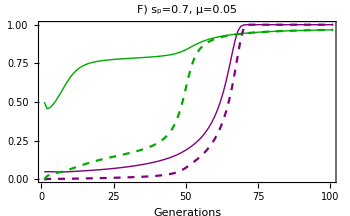

```mathematica
Loop;Fig6=ListPlot[{AlleleFreqA[1],AlleleFreqA[2],AlleleFreqB[1],AlleleFreqB[2]},FrameLabel->{"Generations",None},PlotLabel->Style["F) s_p=0.7, μ=0.05",20,Black],
PlotRange->{{1,Generations},{0,1.000000000000001}},Joined->True,Frame->{True,True,False,False},PlotStyle->{Directive[Purple, Thick],Directive[Darker[Green], Thick],Directive[Purple, Dashed],Directive[Darker[Green], Dashed]},FrameStyle->Directive[20,Black],ImageSize->{350,280}]
```

## Combined figure

```mathematica
TheLegend=LineLegend[{Directive[Purple, Thick],Directive[Darker[Green], Thick],Directive[Purple, Dashed],Directive[Darker[Green], Dashed]},{"Payload-Target","UD-Target","Payload-Neighbor","UD-Neighbor"},LabelStyle->18];
```

```mathematica
CombinedPlot=Grid[{{Fig1,Null,Null,Fig2,Null},{},{},{Fig3,Null,Null,Fig4,TheLegend},{},{},{Fig5,Null,Null,Fig6,Null}},ItemSize->Full]
```

-Graphics- |  |  | -Graphics- | 
 |  |  |  | 
 |  |  |  | 
-Graphics- |  |  | -Graphics- | 
 |  |  |  | 
 |  |  |  | 
-Graphics- |  |  | -Graphics- |